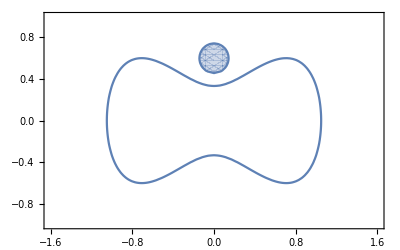

```mathematica
p = x^4-x^2+y^2-1/9;
c1 = (x)^2+(y-0.6)^2-1/49;
CP = ContourPlot[p==0,{x,-1.6,1.6},{y,-1,1}];
RP1 = RegionPlot[c1≤ 0,{x,-1.6,1.6},{y,-1,1}];
Show[RP1, CP,AspectRatio-> 1/1.6]
```

```mathematica
<<ToMatlab`
```

```mathematica
c1/.x-> "x_1"/.y-> "x_2"//ToMatlab//TextForm
```

(-1/49)+x_1.^2+((-0.6E0)+x_2).^2;